```mathematica
SetDirectory[NotebookDirectory[]]
```

## First set

```mathematica
rawdata = Import["DataForPlotting\\SI_CV_vs_N1_data_1.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{23324,2}

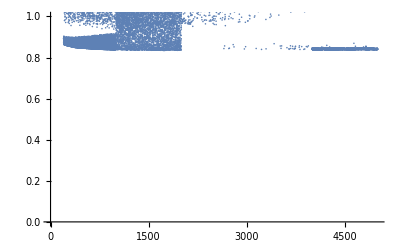

```mathematica
ListPlot[rawdata,PlotRange->{{0,5000},{0,1}}]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.02}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]/5000,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.171457,1.22547}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,23324}];
```

```mathematica
Dimensions[densADJ]
```

{1800,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]*5000,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

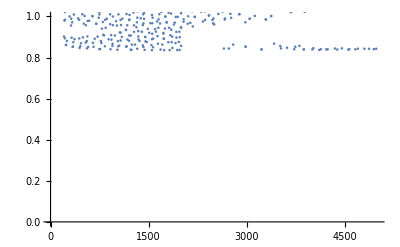

```mathematica
ListPlot[densADJrescaled,PlotRange->{{0,5000},{0,1}}]
```

```mathematica
Export["DataForPlotting\\SI_CV_vs_N1_densADJ_1.txt",densADJrescaled, "Table"]
```

## Second set

```mathematica
rawdata = Import["DataForPlotting\\SI_CV_vs_N1_data_2.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{4078,2}

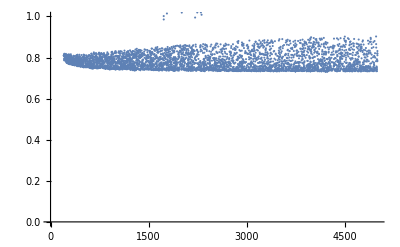

```mathematica
ListPlot[rawdata,PlotRange->{{0,5000},{0,1}}]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.02}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]/5000,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.962478,0.835389}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,10000}];
```

```mathematica
Dimensions[densADJ]
```

{425,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]*5000,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

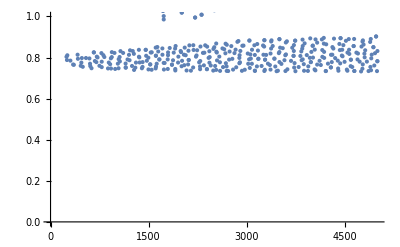

```mathematica
ListPlot[densADJrescaled,PlotRange->{{0,5000},{0,1}}]
```

```mathematica
Export["DataForPlotting\\SI_CV_vs_N1_densADJ_2.txt",densADJrescaled, "Table"]
```

## Third set

```mathematica
rawdata = Import["DataForPlotting\\SI_CV_vs_N1_data_3.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{12662,2}

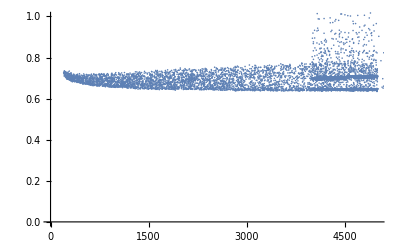

```mathematica
ListPlot[rawdata,PlotRange->{{0,5000},{0,1}}]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.02}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]/5000,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.803166,0.690389}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,10000}];
```

```mathematica
Dimensions[densADJ]
```

{550,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]*5000,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

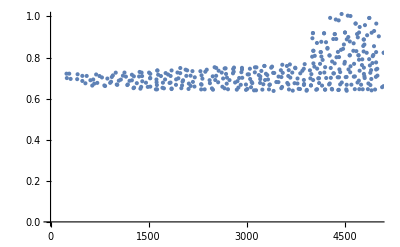

```mathematica
ListPlot[densADJrescaled,PlotRange->{{0,5000},{0,1}}]
```

```mathematica
Export["DataForPlotting\\SI_CV_vs_N1_densADJ_3.txt",densADJrescaled, "Table"]
```

## Fourth set

```mathematica
rawdata = Import["DataForPlotting\\SI_CV_vs_N1_data_4.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{19303,2}

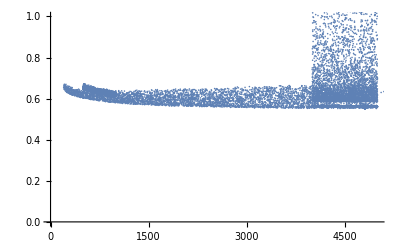

```mathematica
ListPlot[rawdata,PlotRange->{{0,5000},{0,1}}]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.02}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]/5000,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.21235,0.623992}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,10000}];
```

```mathematica
Dimensions[densADJ]
```

{806,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]*5000,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

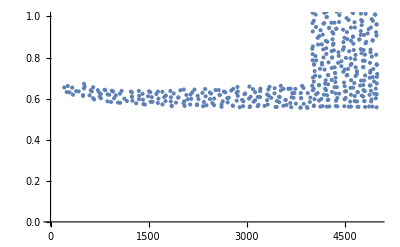

```mathematica
ListPlot[densADJrescaled,PlotRange->{{0,5000},{0,1}}]
```

```mathematica
Export["DataForPlotting\\SI_CV_vs_N1_densADJ_4.txt",densADJrescaled, "Table"]
```